# Fatter Skinnier Potential

## Potential

Pot: (65536.00000000001 + x*(-5.820766091346741*^-11 + x*(-511999.9999999999 + x*(640000. + x*(700000. + x*(-2.45*^6 + x*(2.734375*^6 + x*(-1.66015625*^6 + x*(587463.37890625 + x*(-114440.91796875 + 9536.7431640625*x))))))))))/(65536. + x^8)

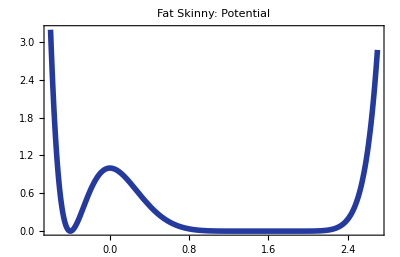

```mathematica
Pot=2^-26((8-5 x)^8 (2.+5 x)^2)/(1+(x/4)^8);

Print["Pot: ",InputForm[HornerForm[Pot]]]

Plot[Pot,{x,-0.6,2.7},PlotRange->All,Frame->True,PlotLabel->"Fat Skinny: Potential"]
```

```mathematica
NIntegrate[Exp[-Pot/0.25],{x,0,∞}]/NIntegrate[Exp[-Pot/0.25],{x,-∞,∞}]
```

0.919018

## Force

Force: (x*(6.7108863999999985*^10 + x*(-1.2582912*^11 + x*(-1.8350079999999997*^11 + x*(8.02816*^11 + x*(-1.0752*^12 + x*(7.616*^11 + x*(-3.07999475712*^11 + x*(6.75*^10 + x*(-6.253071999999999*^9 + x*(3.2000000000000005*^6 + x*(2.7999999999999995*^6 + x*(-7.35*^6 + x*(5.468750000000002*^6 + x*(-1.6601562500000002*^6 + (114440.91796875 - 19073.486328125*x)*x^2)))))))))))))))/(4.294967296*^9 + x^8*(131072. + x^8))

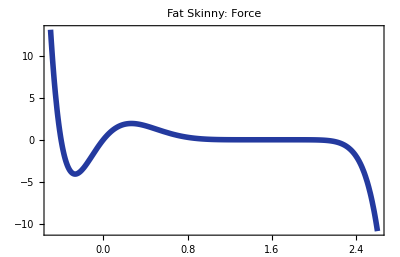

```mathematica
Force=-D[Pot,x];

Print["Force: ",InputForm[HornerForm[Force]]]

Plot[Force,{x,-0.5,2.6},PlotRange->All,Frame->True,PlotLabel->"Fat Skinny: Force"]
```

## Hessian

Hessian: (-4.398046511104*^15 + x*(1.6492674416640008*^16 + x*(3.607772528639999*^16 + x*(-2.10453397504*^17 + x*(3.52321536*^17 + x*(-2.994733056*^17 + x*(1.4129537548183142*^17 + x*(-3.538944*^16 + x*(3.6892185722880005*^15 + x*(-3.8587596800000015*^12 + x*(-4.404019199999996*^12 + x*(1.5414067199999994*^13 + x*(-1.6486400000000002*^13 + x*(9.1392*^12 + x*(-2.7719952814079995*^12 + x*(4.2*^11 + x*(-2.2521503999999992*^10 + x*(1.9199999999999978*^7 + x*(1.4000000000000024*^7 + x*(-2.940000000000005*^7 + x*(1.640625*^7 + x*(-3.3203125000000005*^6 + x*(1.1641532182693481*^-8 + 19073.486328125*x^2)))))))))))))))))))))))/(2.81474976710656*^14 + x^8*(1.2884901888*^10 + x^8*(196608. + x^8)))

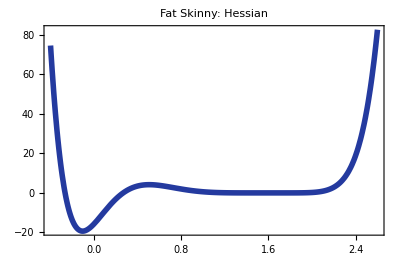

```mathematica
Hess=D[Pot,{x,2}];

Print["Hessian: ",InputForm[HornerForm[Hess]]]

Plot[Hess,{x,-0.4,2.6},PlotRange->All,Frame->True,PlotLabel->"Fat Skinny: Hessian"]
```